```mathematica
a2=ReadList["/home/jirka/CPX/gaps2.txt"]//Sort;
a=ReadList["/home/jirka/CPX/gaps.txt"];
```

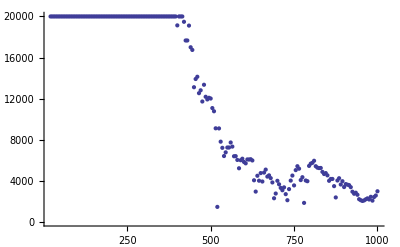

```mathematica
sampleSize={#[[1]],Length[#[[2]]]}&/@a2;
ListPlot[sampleSize,PlotRange->{0,20000}]
```

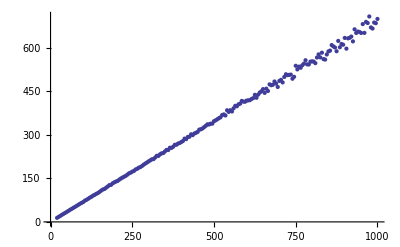

```mathematica
prumerny={#[[1]],Mean[N[#[[2]]]]}&/@a2;
ListPlot[prumerny]
(* prumerny mezery  *)
```

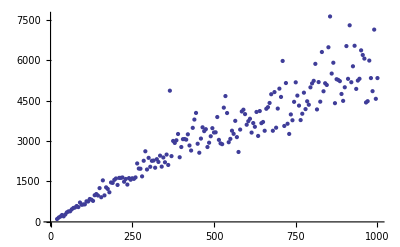

```mathematica
maxs={#[[1]],Max[N[#[[2]]]]}&/@a2;
ListPlot[maxs]
(* velikosti nejvetsi mezery nalezene mezi prvnima 20k prvocislama *)
```

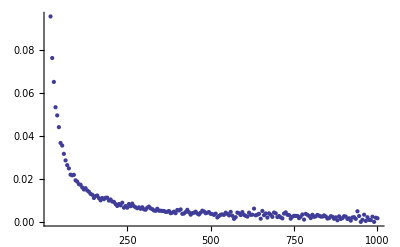

```mathematica
twins={#[[1]],If[Length[#[[2]]]>0,Count[#[[2]],2]/Length[#[[2]]]//N,0]}&/@a2;
ListPlot[twins,PlotRange->Full]
```

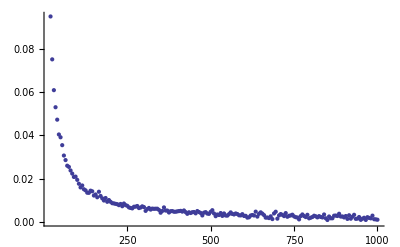

```mathematica
cousins={#[[1]],If[Length[#[[2]]]>0,Count[#[[2]],4]/Length[#[[2]]]//N,0]}&/@a2;
ListPlot[cousins,PlotRange->Full]
```

```mathematica
c=Module[{gaps,coef},gaps=Sort[#[[2]]];coef=(100./Length[gaps]);Table[{#[[1]],i*coef,gaps[[i]]},{i,1,Length[gaps]}]]&/@a2;
```

Sort::normal: Nonatomic expression expected at position 1 in Sort[pckl].

```mathematica
csample=RandomSample[Flatten[c,1],10000];
```

```mathematica
ListPlot3D[csample,PlotRange->Automatic]
(*pocet bitu X distribuce X velikostMezery *)
```

-Graphics3D-

```mathematica
ListPlot3D[csample,PlotRange->Full]
```

-Graphics3D-

```mathematica
Length[Flatten[c,1]] (*pocet mezer*)
Length[csample] (* z toho zobrazenejch *)
```

2298749

10000